```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
T1[t_]:= t*IdentityMatrix[10]
```

```mathematica
T[t_,m_]:=T[t,m]=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=t*IdentityMatrix[m];MAT]
```

```mathematica
Clear[LEFT]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardul/PhD_new/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[-0,3,0.01]}]
```

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+01]]](*Module[{J=Inverse[β[ω,0.0001,1,0,m]],A:=Inverse[β[ω,0.0001,1,0,m]],T:=T1[1]},Do[J=Inverse[IdentityMatrix[m]-A.T.J.T].A,50000];J=J]*)
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
50-5+1
```

46

```mathematica
dist[total_,concentration_,area_]:=dist[total,concentration,area]=Table[SortBy[Join[RandomSample[Join[s[1,100,1,area]],concentration],RandomSample[Join[s[1,100,50-area+1,50]],total-concentration]],First],1000]
```

```mathematica
TLD[t_]:=Module[{sizeoflead=10},Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,Table[{a,a},{a,1,sizeoflead}]->t]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,50]]
```

```mathematica
SLLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
SRLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
device1[ω_,sizeoflead_]:=Module[{},Inverse[IdentityMatrix[50]-g[ω,0.0001,1,0].T[1,sizeoflead].SLLEAD[ω,sizeoflead].T[1,sizeoflead]].g[ω,0.0001,1,0]]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,total_,concentration_,number_,size_,area_]:= Module[{sizeoflead=10},
recurs=Module[{J1= device1[ω,sizeoflead]},
Do[
J1=Inverse[IdentityMatrix[50]-Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[dist[total,concentration,area][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[total,concentration,area][[number]][[loc1,2]],dist[total,concentration,area][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]].T[1,50].J1.T[1,50]].Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[dist[total,concentration,area][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[total,concentration,area][[number]][[loc1,2]],dist[total,concentration,area][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]],{unitcell,size}];J1=J1];ir=Inverse[IdentityMatrix[50]-SRLEAD[ω,sizeoflead].TLD[1].recurs.TLD[1]].SRLEAD[ω,sizeoflead];il=Inverse[IdentityMatrix[50]-recurs.TLD[1].SRLEAD[ω,sizeoflead].TLD[1]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1].recurs;
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[1].grr1.TLD[1]-TLD[1].GNON1.TLD[1].GNON1]];If[TRA>10,10,TRA]]
```

```mathematica
Monitor[Table[Monitor[Table[Export["/home/shardul/PhD_new/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/size_"<>ToString[area]<>"_asy_"<>ToString[conc]<>"_.dat",Monitor[Table[{ω,Mean[ParallelTable[CA[ω,0.0001,1,0,1,100,conc,n,100,area],{n,500}]]},{ω,Range[0,2,0.01]}],ω]],{conc,5,45,5}],conc],{area,Range[15,25,5]}],area]
```

$Aborted

```mathematica
Monitor[Table[{Abs[50-2conc],Mean[ParallelTable[CA[1.1,0.0001,1,0,1,conc,NUM],{NUM,2800}]]},{conc,5,25,5}],conc]
```

{{40,2.28866},{30,2.12017},{20,1.978},{10,1.83911},{0,1.7417}}

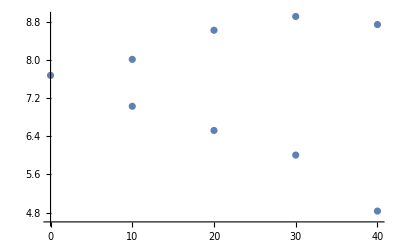

```mathematica
ListPlot[{{40,4.829849658447235},{30,6.003517916592463},{20,6.5187734750574},{10,7.025099935460786},{0,7.672864430779159},{10,8.008427000679896},{20,8.617856366184366},{30,8.907050160143944},{40,8.737279977038465}}]
```

```mathematica
Monitor[Table[{Abs[50-2conc],Mean[ParallelTable[CA[1.1,0.0001,1,0,1,conc,NUM],{NUM,2800}]]},{conc,5,25,5}],conc]
```

{{40,2.28346},{30,2.09785},{20,1.96066},{10,1.82435},{0,1.73556}}

```mathematica
Monitor[Table[Monitor[Table[Mean[ParallelTable[CA[0,0.0001,1,0,1,conc,NUM],{NUM,800}]],{conc,10,40,5}],conc],{w,0.15,2.5,0.05}],w]
```

```mathematica
Table[Table[%192[[x]][[y]],{x,48}],{y,7}]
```

{{4.6214,4.49861,3.829,2.59905,3.17528,3.86811,4.02968,4.07654,3.90149,3.64119,2.87165,2.0812,2.77187,3.34522,3.4934,3.50616,3.53378,3.51402,3.35798,3.14829,2.18362,1.95484,2.46271,2.80115,2.90021,3.01799,3.11643,3.00477,2.87849,2.80435,2.62229,1.92814,1.60777,1.97384,2.32676,2.35852,2.51411,2.3954,2.56826,2.45514,2.35055,2.32691,1.85888,1.33063,1.35443,1.78297,1.76864,1.96775},{4.33362,4.28451,3.65421,2.48463,3.05881,3.64873,3.90528,3.95238,3.79855,3.54085,2.81557,2.10181,2.72942,3.2259,3.39545,3.4235,3.45704,3.40607,3.27574,3.06203,2.19564,1.72095,2.40833,2.70736,2.88095,2.96631,3.05755,2.94044,2.85645,2.76469,2.58436,1.88212,1.60992,1.91282,2.26331,2.30806,2.46108,2.36336,2.51082,2.44859,2.32211,2.30189,1.81118,1.31891,1.36796,1.70723,1.72491,1.92687},{4.05927,3.90084,3.46928,2.35624,2.85428,3.50537,3.74376,3.85284,3.66124,3.40983,2.72434,1.98956,2.57688,3.13929,3.35749,3.36658,3.4045,3.35705,3.17311,3.04958,2.12756,1.75452,2.3086,2.60361,2.80026,2.9338,3.02138,2.92076,2.75983,2.71878,2.51075,1.88732,1.52349,1.7864,2.2016,2.25722,2.40589,2.34305,2.45555,2.37953,2.26595,2.26477,1.76416,1.36615,1.34735,1.64275,1.72294,1.88871},{3.78957,3.68506,3.27048,2.11096,2.63585,3.32021,3.62952,3.73051,3.58918,3.30201,2.70441,2.01794,2.52319,3.0112,3.26368,3.27124,3.3474,3.30542,3.14649,2.9278,2.03232,1.74645,2.21837,2.51134,2.79036,2.87943,2.98656,2.86142,2.74012,2.64954,2.48658,1.80136,1.54686,1.7389,2.17066,2.21206,2.34702,2.32911,2.41912,2.35456,2.23208,2.2248,1.72577,1.37758,1.33071,1.55445,1.67026,1.84684},{3.56543,3.42147,3.16444,2.02137,2.61748,3.20757,3.46582,3.62119,3.45577,3.22442,2.54368,1.95299,2.4244,2.88324,3.19442,3.22897,3.28097,3.25732,3.07707,2.88047,1.99072,1.66346,2.18255,2.44133,2.71176,2.83265,2.89871,2.82571,2.70823,2.61606,2.46259,1.80449,1.52532,1.72538,2.10988,2.18195,2.33831,2.32836,2.4099,2.35113,2.19648,2.21727,1.70109,1.39324,1.25649,1.50531,1.64176,1.81458},{3.22955,3.32806,2.93941,1.97808,2.45268,3.15104,3.3712,3.56188,3.35367,3.14489,2.54555,2.06646,2.43091,2.82939,3.1606,3.15637,3.22879,3.18404,3.02397,2.78417,1.95747,1.71474,2.11665,2.42153,2.66159,2.82276,2.88929,2.76312,2.66954,2.60283,2.43621,1.80577,1.39588,1.6801,2.08966,2.14376,2.30097,2.28204,2.36072,2.32347,2.19884,2.15805,1.71767,1.35327,1.26735,1.45465,1.59569,1.77566},{3.15406,3.09339,2.77489,1.84165,2.36649,3.04699,3.23433,3.45925,3.2658,3.07058,2.39237,2.00071,2.40256,2.73547,3.06137,3.06949,3.15843,3.09147,2.96276,2.77614,1.93027,1.69347,2.05646,2.34147,2.65291,2.79865,2.82722,2.76232,2.66542,2.53481,2.39863,1.76527,1.45166,1.70707,2.0267,2.13642,2.26872,2.29302,2.3403,2.30578,2.1644,2.14108,1.69754,1.38679,1.24713,1.42384,1.58546,1.75497}}

```mathematica
Monitor[ParallelTable[CA[w,0.0001,1,0,1,35,815],{w,0.15,2.5,0.05}],w]
```

{0.275244,4.14285,0.909103,0.122606,4.12067,2.65614,2.745,3.83633,2.85316,3.59692,0.0771131,3.57862,3.0405,3.87462,3.26833,3.01125,2.70894,3.59705,2.47593,2.48652,2.19539,1.74397,3.09504,3.2197,2.38288,2.78414,2.89086,2.59482,2.05533,2.28381,2.2142,2.38442,1.26639,2.459,2.24836,2.39439,2.54447,2.08324,2.45536,2.25309,2.71297,2.47284,0.826396,0.529049,0.0362609,1.74702,2.32322,2.43653}

```mathematica
a1[n_]:=a1[n]=Monitor[ParallelTable[CA[w,0.0001,1,0,1,15,n],{w,0.15,2.5,0.05}],w]
```

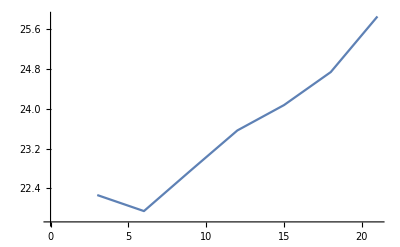
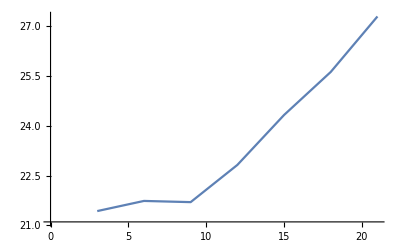
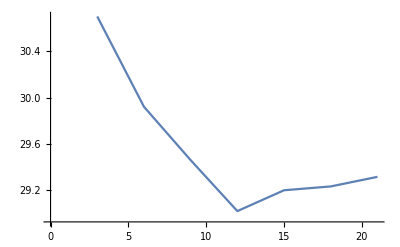
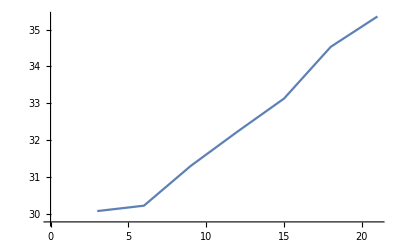
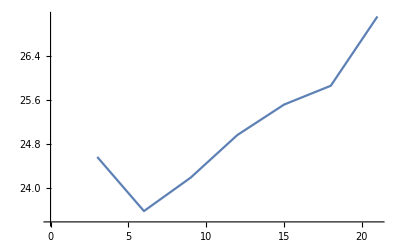
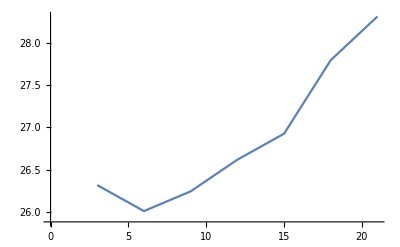
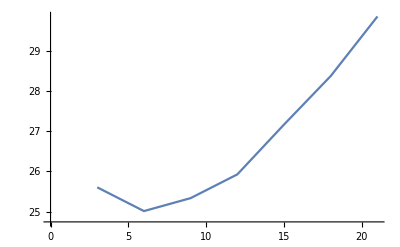
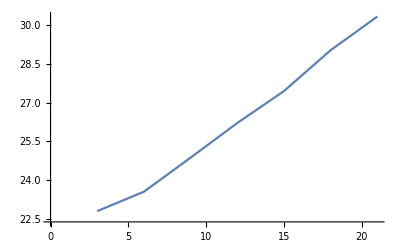

```mathematica
Table[ListLinePlot[Table[{3x,Total[Abs[%197[[x]]-a1[n]]]},{x,7}]],{n,900,910}]
```

```mathematica
%211[[1]]
```

-Graphics-

```mathematica
{{3, 22.26}, {6., 21.94395836001202}, {9., 22.760099612482655}, {12., 23.56586619067679}, {15., 24.076943971933915}, {18., 24.74044075631211}, {21., 25.859098314960587}}
```

Syntax::tsntxi: "ToExpression[{{3.,22.266587298588163},{6.,21.94395836001202},{9.,22.760099612482655},{12.,23.56586619067679},{15.,24.076943971933915},{18.,24.74044075631211},{21.,25.859098314960587}}]" is incomplete; more input is needed.

```mathematica
{{3,22.6},{6,21.94},{9,22.76},{12,23.56},{15,24.076},{18,24.74},{21,25.859}}
```

```mathematica
{{3,22.6},{6,21.74},{9,22.76},{12,23.56},{15,24.076},{18,24.74},{21,25.859}}
```

{{3,22.6},{6,21.74},{9,22.76},{12,23.56},{15,24.076},{18,24.74},{21,25.859}}

```mathematica
Interpolation[%23]
```

InterpolatingFunction[…]

```mathematica
Export["misfit_sm.dat",Table[{x,%24[x]/250},{x,3.,21.}]]
```

misfit_sm.dat

```mathematica
Export["misfit_sm_line.dat",Table[{5,x},{x,0,0.101,0.00001}]]
```

misfit_sm_line.dat

```mathematica
ListLinePlot[%197]
```

```mathematica
Monitor[Table[Export["/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/ϵ1_1_32_33_50_"<>ToString[conc]<>"_.dat",Monitor[Table[{ω,Mean[ParallelTable[CA[ω,0.0001,1,0,1,conc,n],{n,800}]]},{ω,Range[0,3,0.01]}],ω]],{conc,5,45,5}],conc]
```

{/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/ϵ1_1_32_33_50_5_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/ϵ1_1_32_33_50_10_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/ϵ1_1_32_33_50_15_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/ϵ1_1_32_33_50_20_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/ϵ1_1_32_33_50_25_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/ϵ1_1_32_33_50_30_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/ϵ1_1_32_33_50_35_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/ϵ1_1_32_33_50_40_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/ϵ1_1_32_33_50_45_.dat}

```mathematica
transmission= Table[{x,Import["/home/shardul/PhD_new/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/full_device/ϵ1_conc_"<>ToString[x]<>"_.dat"]},{x,Range[10,140,10]}]
```

{{10,{{0.,8.20345},{0.01,7.19567},{0.02,6.44567},{0.03,5.6569},{0.04,5.4354},{0.05,4.52895},{0.06,4.45416},{0.07,4.43167},{0.08,5.01419},{0.09,3.94818},{0.1,3.81156},{0.11,4.57462},{0.12,5.2241},{0.13,4.61557},273,{2.87,1.78978},{2.88,0.992149},{2.89,1.16958},{2.9,1.21996},{2.91,1.55008},{2.92,1.31153},{2.93,1.15746},{2.94,1.67728},{2.95,1.43777},{2.96,1.51666},{2.97,1.44988},{2.98,1.24043},{2.99,1.61067},{3.,1.74349}}},12,{140,{1}}}
 |  |  |  |

```mathematica
Dimensions[transmission]
```

{14,301,2}

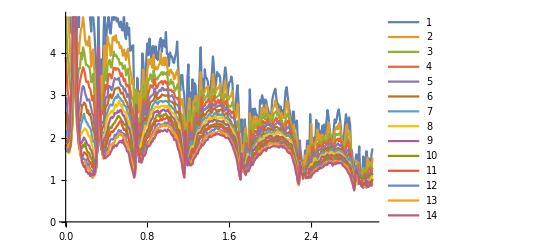

```mathematica
ListLinePlot[transmission,PlotLegends->Automatic]
```

```mathematica
Dimensions[transmission]
```

{9,301,2}

```mathematica
input= Monitor[Table[ParallelTable[{ω,CA[ω,0.0001,1,0,1,25,n]},{ω,Range[0,3,0.01]}],{n,800,900}],n]
```

{{{0.,4.42012},{0.01,0.235216},{0.02,0.761476},{0.03,1.1882},{0.04,3.02967},{0.05,2.94666},{0.06,2.93727},{0.07,3.03028},{0.08,9.73197},{0.09,4.12091},{0.1,12.1285},{0.11,1.11262},{0.12,1.18225},{0.13,1.21805},273,{2.87,1.39886},{2.88,1.06976},{2.89,0.653055},{2.9,1.21809},{2.91,0.986789},{2.92,0.0740162},{2.93,1.59202},{2.94,0.062917},{2.95,0.395573},{2.96,0.595838},{2.97,0.409104},{2.98,1.29335},{2.99,1.48228},{3.,0.994835}},99,{1}}
 |  |  |  |

```mathematica
Clear[misfit,d1]
```

```mathematica
misfit[x_,y_,n_]:=Module[{m5=input[[n]]},
ρ1=Table[{transmission[[con,1]],Module[{B1=Transpose[{m5[[1;;301]][[;;,1]],(m5[[1;;301,2]]-transmission[[con,2]][[1;;301,;;]][[;;,2]])^2}]},NIntegrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)(*+NIntegrate[Interpolation[B1][ω],{ω,-3,-0.5}]/((2.5)*100)*)]},{con,14}];lista=ρ1;
{lista,lista[[Position[lista,Min[lista]][[1,1]]]]}]
```

```mathematica
ListLinePlot[{input[[1]],input[[2]]},PlotRange->All]
```

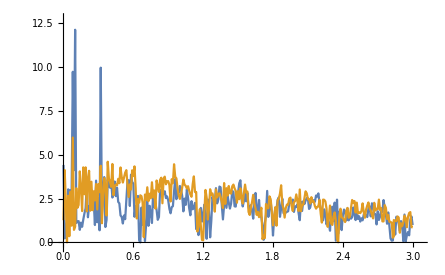

```mathematica
Interpolation[misfit[2.5,0.15,9][[1]]]
```

InterpolatingFunction[…]

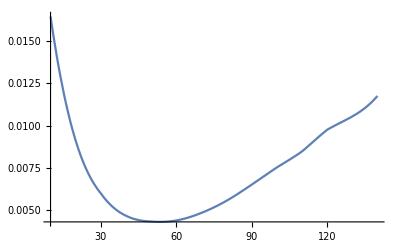

```mathematica
Plot[%65[x],{x,10.,140.}]
```

```mathematica
Table[{x,%65[x]},{x,10.,140.}]
```

{{10.,0.0164765},{11.,0.0154785},{12.,0.0145448},{13.,0.0136731},{14.,0.012861},{15.,0.0121059},{16.,0.0114054},{17.,0.0107572},{18.,0.0101587},{19.,0.00960758},{20.,0.00910131},{21.,0.00863748},{22.,0.00821365},{23.,0.00782738},{24.,0.00747623},{25.,0.00715776},{26.,0.00686953},{27.,0.00660911},{28.,0.00637404},{29.,0.00616189},{30.,0.00597022},{31.,0.00576982},{32.,0.00558664},{33.,0.00541987},{34.,0.00526868},{35.,0.00513226},{36.,0.00500978},{37.,0.00490043},{38.,0.00480339},{39.,0.00471785},{40.,0.00464298},{41.,0.00457409},{42.,0.00451447},{43.,0.00446354},{44.,0.00442072},{45.,0.00438543},{46.,0.00435707},{47.,0.00433507},{48.,0.00431885},{49.,0.00430782},{50.,0.00430139},{51.,0.00428958},{52.,0.00428179},{53.,0.00427799},{54.,0.00427818},{55.,0.00428235},{56.,0.00429047},{57.,0.00430255},{58.,0.00431856},{59.,0.00433849},{60.,0.00436233},{61.,0.00439185},{62.,0.00442515},{63.,0.00446211},{64.,0.0045026},{65.,0.0045465},{66.,0.0045937},{67.,0.00464406},{68.,0.00469748},{69.,0.00475382},{70.,0.00481297},{71.,0.00487329},{72.,0.00493627},{73.,0.00500188},{74.,0.00507009},{75.,0.00514086},{76.,0.00521418},{77.,0.00529001},{78.,0.00536832},{79.,0.00544909},{80.,0.00553228},{81.,0.00562029},{82.,0.00571052},{83.,0.0058028},{84.,0.00589694},{85.,0.00599277},{86.,0.00609011},{87.,0.00618879},{88.,0.00628864},{89.,0.00638946},{90.,0.0064911},{91.,0.00659273},{92.,0.00669486},{93.,0.00679734},{94.,0.00690004},{95.,0.00700282},{96.,0.00710555},{97.,0.00720809},{98.,0.00731029},{99.,0.00741202},{100.,0.00751315},{101.,0.00760446},{102.,0.00769543},{103.,0.00778648},{104.,0.00787803},{105.,0.00797049},{106.,0.00806426},{107.,0.00815977},{108.,0.00825742},{109.,0.00835763},{110.,0.00846081},{111.,0.00858793},{112.,0.0087176},{113.,0.00884899},{114.,0.00898125},{115.,0.00911357},{116.,0.00924511},{117.,0.00937503},{118.,0.0095025},{119.,0.00962669},{120.,0.00974676},{121.,0.00983292},{122.,0.00991505},{123.,0.00999408},{124.,0.0100709},{125.,0.0101465},{126.,0.0102218},{127.,0.0102976},{128.,0.010375},{129.,0.0104547},{130.,0.0105379},{131.,0.0106253},{132.,0.0107178},{133.,0.0108166},{134.,0.0109223},{135.,0.011036},{136.,0.0111586},{137.,0.011291},{138.,0.0114342},{139.,0.011589},{140.,0.0117563}}

```mathematica
Export["data_subset_misfit1.dat",%63]
```

data_subset_misfit1.dat

```mathematica
Export["data_subset_misfit2.dat",%67]
```

data_subset_misfit2.dat

```mathematica
Table[misfit[2.5,0.15,n][[2]][[1]],{n,100}]
```

{90,40,60,60,40,70,70,50,50,60,30,60,40,70,50,50,30,70,60,70,50,50,40,50,110,40,40,70,80,70,80,40,50,30,40,70,40,50,60,60,40,40,40,30,50,40,60,90,50,40,50,50,50,40,40,50,60,40,70,60,30,40,60,40,60,90,60,60,70,50,40,50,30,40,40,50,40,40,40,50,40,40,30,40,40,50,40,60,40,70,40,60,60,50,40,60,40,40,50,40}

```mathematica
Import["data1.dat"][[Position[Import["data1.dat"],Min[Import["data1.dat"]]][[1,1]]]]
```

{29.,0.00801848}

```mathematica
Import["data2.dat"][[Position[Import["data2.dat"],Min[Import["data2.dat"]]][[1,1]]]]
```

{24,0.00693629}

```mathematica
Import["data3.dat"][[Position[Import["data3.dat"],Min[Import["data3.dat"]]][[1,1]]]]
```

{28,0.0143248}

```mathematica
Export["data4.dat",Table[{28,x},{x,0,0.04,0.0001}]]
```

data4.dat

```mathematica
Export["data5.dat",Table[{24,x},{x,0,0.04,0.0001}]]
```

data5.dat

```mathematica
Export["data6.dat",Table[{29,x},{x,0,0.04,0.0001}]]
```

data6.dat

```mathematica
a[XX_]:=Table[{x,Interpolation[misfit[2.5,0.15,XX][[1]]][x]},{x,10,140,1}]
```

```mathematica
Monitor[Table[a[XX],{XX,100}],XX]
```

{{{10,0.0221006},{11,0.0211167},{12,0.0201987},{13,0.019344},{14,0.01855},{15,0.0178139},{16,0.0171333},{17,0.0165055},{18,0.0159278},{19,0.0153977},111,{131,0.0162026},{132,0.0162646},{133,0.0163282},{134,0.0163938},{135,0.0164617},{136,0.0165323},{137,0.016606},{138,0.0166832},{139,0.0167642},{140,0.0168494}},98,{1}}
 |  |  |  |

```mathematica
Table[{XX,%112[[XX]][[Position[%112[[XX]],Min[%112[[XX]]]][[1,1]]]][[1]]},{XX,100}]
```

{{1,51},{2,50},{3,58},{4,44},{5,56},{6,41},{7,45},{8,45},{9,53},{10,41},{11,86},{12,53},{13,45},{14,56},{15,57},{16,47},{17,47},{18,50},{19,52},{20,53},{21,51},{22,43},{23,48},{24,42},{25,44},{26,53},{27,67},{28,56},{29,45},{30,52},{31,46},{32,40},{33,53},{34,58},{35,50},{36,51},{37,45},{38,47},{39,42},{40,48},{41,33},{42,50},{43,53},{44,54},{45,53},{46,37},{47,60},{48,40},{49,39},{50,46},{51,40},{52,57},{53,55},{54,58},{55,38},{56,55},{57,61},{58,42},{59,64},{60,47},{61,45},{62,62},{63,59},{64,45},{65,55},{66,42},{67,66},{68,54},{69,54},{70,46},{71,47},{72,60},{73,51},{74,42},{75,46},{76,41},{77,49},{78,44},{79,36},{80,60},{81,62},{82,60},{83,69},{84,56},{85,68},{86,38},{87,48},{88,46},{89,51},{90,36},{91,53},{92,67},{93,48},{94,48},{95,50},{96,58},{97,42},{98,45},{99,43},{100,45}}

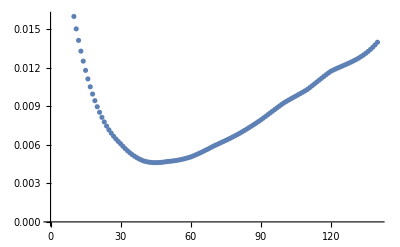

```mathematica
b=Table[{x,Interpolation[misfit[2.5,0.15,7][[1]]][x]},{x,10,140}]//ListPlot
```

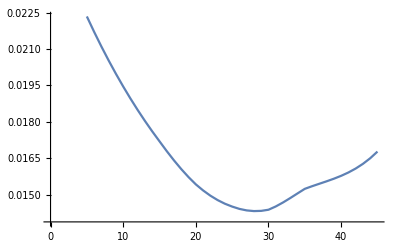

```mathematica
ListPlot[a,Joined->True]
```

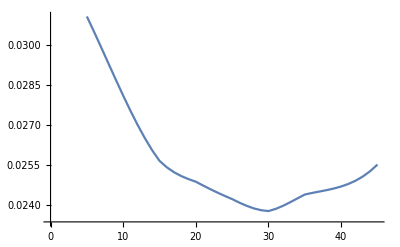

```mathematica
ListPlot[a,Joined->True]
```

```mathematica
Export["data2.dat",%98]
```

data2.dat

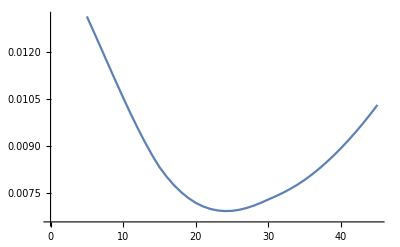

```mathematica
ListPlot[a,Joined->True]
```

```mathematica
Export["data1.dat",%91]
```

data1.dat

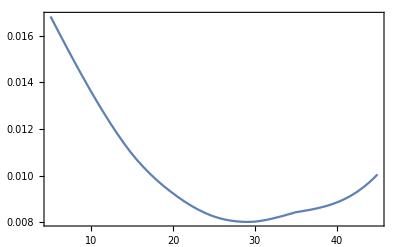

```mathematica
Plot[%88[x],{x,5.,45.},Frame->True,PlotRange->All]
```

```mathematica
Table[misfit[2.5,0.15,n][[2]][[1]],{n,100}]
```

{50,50,60,40,60,40,50,50,50,40,90,50,40,60,60,50,50,50,50,50,50,40,50,40,40,50,70,60,40,50,50,40,50,60,50,50,50,50,40,50,30,50,50,50,50,40,60,40,40,50,40,60,60,60,40,60,60,40,60,50,40,60,60,40,60,40,70,50,50,50,50,60,50,40,50,40,50,40,40,60,60,60,70,60,70,40,50,50,50,40,50,70,50,50,50,60,40,50,40,50}

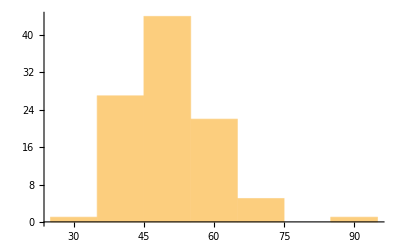

```mathematica
Histogram[%98]
```

```mathematica
PDF[%40,X]
```

PDF[{40,50,40,60,70,50,50,60,50,50,40,30,40,50,30,40,40,40,50,40,50,50,40,40,40,40,50,50,50,60,70,50,60,50,40,40,50,40,40,50,40,50,40,50,50,60,40,70,60,50,50,50,50,50,50,40,50,40,60,50,50,50,40,60,50,50,40,40,60,40,40,40,40,40,50,40,50,60,90,70,50,60,70,40,40,40,40,40,50,40,50,40,40,40,50,60,50,40,40,60},X]

```mathematica
Mean[Abs[Table[misfit[1,0.15,n][[2]][[1]],{n,50}]-20]/20]
```

9/40

```mathematica
N[9/40]
```

0.225

```mathematica
N[4/45]
```

0.0888889

```mathematica
N[76/225]
```

0.337778

```mathematica
N[11/60]
```

0.183333

```mathematica
N[41/200]
```

0.205

```mathematica
d1[x_,n_]:=d1[x,n]=Mean[ParallelTable[misfit[x,y,n][[2]][[1]],{y,0.14,x-0.1,0.02}]]
```

```mathematica
xxx=Monitor[Table[Mean[Table[d1[x,n],{x,Range[0.5,2,0.05]}]],{n,100}],n]
```

{599722352531655697391157312535/14938540618885399512835046208,9021670133260444305417669956605/220343474128559642814316931568,10843853970372967829567945485/302669607319450058810874906,34287959532611720310880743324395/881373896514238571257267726272,341957761447156805018593585/9970744111885589520535632,30384084108818129905508526955175/881373896514238571257267726272,22507110505995037539451843535/533519307817335696886965936,160740759429084144340608970195/3815471413481552256524968512,16830942729358968392559159047305/440686948257119285628633863136,32715102581945493546158046801865/881373896514238571257267726272,33894720055159197355031103395305/881373896514238571257267726272,75973561099695133846473763015/2064107485981823351890556736,1056974806767096638563424722585/30392203328077192112319576768,16761018235531386269966407970545/440686948257119285628633863136,3289206218229919089298260980/103544865661917125382667731,6827322898673501201228702721245/220343474128559642814316931568,2612254709437050623362590575755/62955278322445612232661980448,1560929606422202554056378313435/41970185548297074821774653632,451046158652014037793104995/15848057980261059647881248,470993772336065275825621745/11632534797199854440624904,321802160210067855407222624765/8993611188920801747523140064,3312375610211654132265787104925/110171737064279821407158465784,14822642469162937478328139521925/440686948257119285628633863136,1297987372456658018008663418735/46388099816538872171435143488,1338903400152200392780224035/42461526064182616527304896,642244161544073583307253721025/21496924305225331006274822592,1695683836980227957651340219865/48965216473013253958737095904,570083747117810459930941227125/14448752401872763463233897152,812629206243961126581561192805/27542934266069955351789616446,397836215073392167866748561225/9477138672196113669432986304,41651376110542837272414782305/1127076594007977712605201696,26324459278214313784288938232285/881373896514238571257267726272,2794593835477523009214770718205/97930432946026507917474191808,4535072031453821967987573952765/146895649419039761876211287712,2307872776606107019477149333655/80124899683112597387024338752,1302324018859794508315624973365/38320604196271242228576857664,32915827270045656038849088055115/881373896514238571257267726272,31443713684791843573479461312425/881373896514238571257267726272,394391327462205886469071016185/11156631601446057864016047168,40710072839557663793225094745/1034476404359434942790220336,29438251836111948900976622329475/881373896514238571257267726272,1932420752386217196704378944255/48965216473013253958737095904,36483912052225912962875045530825/881373896514238571257267726272,27405694343008934649384220534895/881373896514238571257267726272,8569296809676407607098304388375/293791298838079523752422575424,439093833040826134467475713665/12773534732090414076192285888,18187183455558746098664428271945/440686948257119285628633863136,8465528453164347175871121260015/220343474128559642814316931568,14386984231683314143336966934705/440686948257119285628633863136,2871313265631325516079102229475/80124899683112597387024338752,322583705564323204393634259385/7869409790305701529082747556,273140902347054681069907683385/9580151049067810557144214416,9856701513874051134599024654785/293791298838079523752422575424,14045199531772199791975785566785/440686948257119285628633863136,88931597663372643651735462725/3070989186460761572324974656,1098267632146948432316143825/28828505430093172775235264,16805323870910838157184493951515/440686948257119285628633863136,357848602664929649587096765/10409272209399076096670301,505408107755343170263600365775/15738819580611403058165495112,10126932172830907114105142950445/293791298838079523752422575424,3536404941008711055491393045/99320925908748993831109728,7629863523355061754745859525/209054529533737801531609992,3266143360725590077696152830/75253918759753976371009881,26543444346740751554411506262825/881373896514238571257267726272,3504694136911757685642942730775/97930432946026507917474191808,9680604229205489818283890505/225646158861812230224594912,884202917945829369950034720905/20985092774148537410887326816,30288951062318268454742583537125/881373896514238571257267726272,2457770006536705515850951014415/67797992039556813173635978944,321891708922912699795878772175/8902766631456955265224926528,96986869562865306584401585225/2728711753914051304202067264,3875869338331431774997374985/107694757638592200789011208,1484337733785027377116942836065/46388099816538872171435143488,14945842020542042368508182393505/440686948257119285628633863136,1954815701912677313322788176945/51845523324366974779839278016,2262973692037766297319597455/56386277046525402805787712,29302406072198997067885154987125/881373896514238571257267726272,1420563610984154496283021584475/41970185548297074821774653632,1146653927146085209426240148825/30392203328077192112319576768,1077461576962950077655296345095/38320604196271242228576857664,21723129829956486973258109765/618942343057751805658193628,8088749126688465489345625670/225761756279261929113029643,7464090600526423370744586491335/220343474128559642814316931568,28118086302104269691455100679265/881373896514238571257267726272,16981682645856575215715923863685/440686948257119285628633863136,342637104539412134516070310855/12961380831091743694959819504,20096212756342913127975161465/651421948643191848674994624,938511215564839277983789267445/26708299894370865795674779584,193743528503385117634035771925/5649832669963067764469664912,850533962607327827543620582055/20985092774148537410887326816,572045712061129169682382798615/17281841108122324926613092672,32591160670819514326097277601165/881373896514238571257267726272,68121561485415790886218744055/1656717850590674006122683696,8655382690188430350157693437955/293791298838079523752422575424,29605839996965536397970559477055/881373896514238571257267726272,150389908597328259481414255/3994117391349169663282704,252120622813245295410815/5685398628651032406192,5524569954147265972481408554715/146895649419039761876211287712,870514260327698359025226166445/24482608236506626979368547952,1058272348667736409439883611095/28431416016588341008298958912}

```mathematica
Mean[Abs[N[xxx]-30]/30]
```

0.191735

```mathematica
N[xxx]
```

{23.014,28.3189,14.5247,13.7986,23.1032,13.7483,18.6462,13.1291,29.7878,23.1883,30.1202,36.1548,31.3528,16.1085,29.1795,16.1216,22.3573,32.8634,19.2807,16.4107,19.5831,30.7264,22.6833,21.6804,27.4913,29.4556,24.4431,23.1739,27.2662,32.4934,25.3999,19.5525,34.7362,32.4185,20.8132,26.1215,16.377,35.8534,36.6907,35.4707,28.5669,32.8039,31.7473,21.9928,18.8744,23.3886,23.1019,31.8532,27.301,33.9823,25.7717,34.3944,32.0499,33.379,24.4201,24.149,17.5496,32.3693,25.5978,32.1446,25.9389,19.6152,24.6996,29.5536,25.2341,25.84,31.9351,34.4486,34.5559,28.4858,30.2575,30.5738,21.0274,22.1735,26.1189,20.9803,23.1527,25.1697,20.4477,24.6901,21.6117,34.9742,29.179,25.8353,33.46,24.1217,30.361,19.5732,27.6453,25.9651,17.8753,17.8248,26.2028,25.9211,21.3561,21.0437,25.1346,22.0178,29.4708,32.9059}

```mathematica
Mean[%68]
```

25.8645

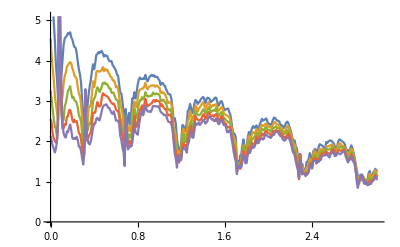

```mathematica
ListLinePlot[Table[transmission[[x,2]],{x,Range[1,9,2]}]]
```

```mathematica
{{1, 1, 0, 0}, {1, 0, 1, 0}, {0, 0, 1, 1}, {1, 0, 0, 1}}{{0}, {0}, {0}, {0}}
```

{{1,1,0,0},{1,0,1,0},{0,0,1,1},{1,0,0,1}}

```mathematica
Inverse[{{1,1,0,0},{1,0,1,0},{0,0,1,1},{1,0,0,1}}].{{28},{24},{22},{29}}
```

{{31/2},{25/2},{17/2},{27/2}}

```mathematica
15
```

15

```mathematica
13
```

13

```mathematica
9
```

9

```mathematica
14
```

14

```mathematica
Det[{{1,1,0,0},{1,0,1,0},{0,0,1,1},{1,0,0,1}}]
```

-2

```mathematica
{{28}, {24}, {22}, {29}}
```

{{28},{24},{22},{29}}